%%% Zerilli equation AXIAL modes, %%%  determination of  λ0[xi, ω] and s0[xi, ω] :

%%% n = 2 -> S. Chandrasekhar notation :

```mathematica
n=2
```

2

%%% yeh = obtained from g00 = 0.
%%% For nn = 4 of pc - GR :

%%% Mass function and its derivatives :

```mathematica
m[y]=1-27/(32 y^3)
```

1-27/(32 y^3)

```mathematica
m'[y]=FullSimplify[D[m[y],y]]
```

81/(32 y^4)

```mathematica
m''[y]=FullSimplify[D[m'[y],y]]
```

-81/(8 y^5)

```mathematica
Derivative[3][m][y]=D[m''[y],y]
```

405/(8 y^6)

```mathematica
Derivative[4][m][y]=FullSimplify[D[Derivative[3][m][y],y]]
```

-1215/(4 y^7)

%% Define yeh and Tranlate y to xi

```mathematica
yeh=3/2
```

3/2

```mathematica
y=(3/2)/(1-xi)
```

3/(2 (1-xi))

%%% calculating the mass functiosn in terms of xi :

```mathematica
M[xi]=FullSimplify[1-27/(32 y^3)]
```

1+1/4 (-1+xi)^3

```mathematica
M'[xi]=81/(32 y^4)
```

1/2 (1-xi)^4

```mathematica
M''[xi]=-81/(8 y^5)
```

-4/3 (1-xi)^5

```mathematica
Derivative[3][M][xi]=405/(8 y^6)
```

40/9 (1-xi)^6

```mathematica
Derivative[4][M][xi]=-1215/(4 y^7)
```

-160/9 (1-xi)^7

%%% Potential :

```mathematica
V[xi_]=FullSimplify[((y^2-2 M[xi] y)/y^5)(6 y - 6 M[xi]+2 y M'[xi])]
```

8/27 (-1+xi)^2 xi^2 (6+(-4+xi) xi) (2+xi (-2+xi (6+(-4+xi) xi)))

%%% xi : [0, 1]

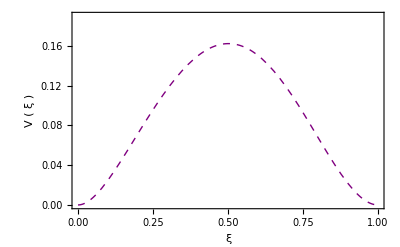

```mathematica
Plot[V[xi],{xi,0,1},Frame->True,PlotRange->{0,0.19},FrameLabel->{Style[" ξ ",Large,Black],Style[" V ( ξ ) ",Large,Black]}, PlotStyle->{{Purple, Thick, Dashed},{Purple, Thick,Dashed}}, FrameLabel->Automatic]
```

%%% Coeffcients in differential equation, Eq. (35) :

```mathematica
F1[xi_]:=-(2/(1-xi))(1 -((1-xi)/yeh)(M[xi]-M'[xi] yeh/(1-xi))/(1- 2(1-xi)M[xi]/yeh))
```

```mathematica
F2[xi_]:=- ω^2 /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)
```

```mathematica
F3[xi_]:=-V[xi] /(1-2 (1-xi) M[xi]/yeh)^2  (yeh^2/(1-xi)^4)
```

%%% Asymptotic limit factor :

```mathematica
Zx[xi_]:=( 1-xi)^(-2 ω) xi^{-2 ω}  ⅇ^(ω yeh/(1-xi))ⅇ^(3ω (1-xi)/(4xi))
```

%%% Final Zerilli function, change to P[xi]

```mathematica
Z[xi_]:=Zx[xi] PP[xi]
```

%%% First derivative in xi

```mathematica
ZDy1[xi_]:=D[Z[xi],xi]
```

%%% Second derivative in xi

```mathematica
ZDy2[xi_]:=D[ZDy1[xi],xi]
```

%%% Differential equation :

```mathematica
EQA[xi_]:= ZDy2[xi]+ F1[xi] ZDy1[xi] +( F2[xi] + F3[xi]) Z[xi]
```

%%% Extract coeffcient of second derivative :

```mathematica
cc0= Coefficient[EQA[xi], PP''[xi]]
```

{ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2 ω)}

%%% Divide differential equation by this factor :

```mathematica
EQa[xi_]:=EQA[xi]/cc0
```

%%% CHECK coefficient of second derivative, has to be 1 :

```mathematica
Coefficient[EQa[xi], PP''[xi]]
```

{1}

%%% extract coefficient of first derivative :

```mathematica
Coefficient[EQa[xi], PP'[xi]]
```

{ⅇ^(-(3 ω)/(2 (1-xi))-(3 (1-xi) ω)/(4 xi)) (1-xi)^(2 ω) xi^(2 ω) ((4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(1-2 ω))/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(2-2 ω))/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(3-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-(4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(4-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω)-3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω-4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-1-2 ω) ω+3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)}

%%% Extract coefficient of P[xi]

```mathematica
Coefficient[EQa[xi], PP[xi]]
```

{ⅇ^(-(3 ω)/(2 (1-xi))-(3 (1-xi) ω)/(4 xi)) (1-xi)^(2 ω) xi^(2 ω) (-(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(2-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+(88 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(3-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)-(196 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(4-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+(108 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(5-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)-(116 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(6-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+(76 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(7-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)-(30 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(8-2 ω))/((1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+(20 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(9-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)-(2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(10-2 ω))/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-3-2 ω) ω+3/2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2-2 ω) ω+2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω-(3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(12 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(1-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(12 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(2-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(2-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(29 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(2-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(3-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+(32 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(3-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))+(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(3-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-(2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(4-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))-(8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(4-2 ω) ω)/(3 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi)))-2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω-(2 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2 ω) ω)/(1-4/3 (1+1/4 (-1+xi)^3) (1-xi))+9/16 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-4-2 ω) ω^2+3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-3-2 ω) ω^2-9/4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2-2 ω) ω^2-3 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-2-2 ω) ω^2+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2 ω) xi^(-2-2 ω) ω^2-6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-1-2 ω) ω^2-8 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-1-2 ω) xi^(-1-2 ω) ω^2+9/4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(-2 ω) ω^2-(9 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-4-2 ω) xi^(-2 ω) ω^2)/(4 (1-4/3 (1+1/4 (-1+xi)^3) (1-xi))^2)+6 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-3-2 ω) xi^(-2 ω) ω^2+4 ⅇ^((3 ω)/(2 (1-xi))+(3 (1-xi) ω)/(4 xi)) (1-xi)^(-2-2 ω) xi^(-2 ω) ω^2)}

%%%λ0[y_,om_]:=FullSimplify[Coefficient[EQa[y], PP'[y]]],

```mathematica
FullSimplify[Coefficient[EQa[xi], PP'[xi]]]
```

{((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)}

TAKE AN EXTRA MINUS SIGN IN ORDER TO RELATE TO THE AIM EQUATIONS!

```mathematica
λ0[xi_,ω_]:=-(((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2))
```

```mathematica
λ0[xi,ω]
```

-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)

%%% s0[y_,  om_] := FullSimplify[Coefficient[EQa[y], PP[y]]]

```mathematica
Simplify[Coefficient[EQa[xi], PP[xi]]]
```

{(xi^3 (4800+19960 ω-20802 ω^2)+32 xi^6 (-3-10 ω+8 ω^2)-48 xi^5 (-16-57 ω+50 ω^2)-48 xi (-40-167 ω+96 ω^2)-36 (32+167 ω^2)+xi^4 (-2688-10216 ω+9817 ω^2)+xi^2 (-4416-20176 ω+21409 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2)}

%%% Multiply by (-1) due to shift to the right hand side of the equation :

```mathematica
s0[xi_,ω_]:=-((xi^3 (4800+19960 ω-20802 ω^2)+32 xi^6 (-3-10 ω+8 ω^2)-48 xi^5 (-16-57 ω+50 ω^2)-48 xi (-40-167 ω+96 ω^2)-36 (32+167 ω^2)+xi^4 (-2688-10216 ω+9817 ω^2)+xi^2 (-4416-20176 ω+21409 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2))
```

%%% Copy final results :

```mathematica
s0[xi,ω]
```

-((xi^3 (4800+19960 ω-20802 ω^2)+32 xi^6 (-3-10 ω+8 ω^2)-48 xi^5 (-16-57 ω+50 ω^2)-48 xi (-40-167 ω+96 ω^2)-36 (32+167 ω^2)+xi^4 (-2688-10216 ω+9817 ω^2)+xi^2 (-4416-20176 ω+21409 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2))

```mathematica
λ0[xi, ω]
```

-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2)